## Spherical Harmonics

```mathematica
PlotRange->{{-.45,.45},{-.45,.45},{-0.775,0.775}};
```

```mathematica
Manipulate[Show[
ParametricPlot3D[
{Cos[p]Sin[t],Sin[p]Sin[t],Cos[t]},
{p,0,2 Pi},{t,0,Pi},
Mesh->False,
ViewAngle->Automatic,Axes->False,SphericalRegion->True,Boxed->False,AxesOrigin->{0,0,0},Ticks->None,PlotStyle->Directive[Gray,Opacity[.25]],ColorFunctionScaling->False],
ParametricPlot3D[
{Cos[p]Sin[t],Sin[p]Sin[t],Cos[t]}Abs[Re[SphericalHarmonicY[l,m,t,p]]],
{p,0,2 Pi},{t,0,Pi},
Mesh->False,
ViewAngle->Automatic,Axes->False,SphericalRegion->True,Boxed->False,AxesOrigin->{0,0,0},Ticks->None,ColorFunction -> Function[{x,y,z,p,t},Piecewise[{{RGBColor[.2,.75,.4, 1], Ylm>0}, {RGBColor[0,0,1], Ylm==0}, {RGBColor[.75,.2,.3,1], Ylm<0}}]/.Ylm->Re[SphericalHarmonicY[l,m,t,p]]],ColorFunctionScaling->False]],
{{l,2,"degree l"},0,7,1,Appearance->"Labeled"},
{{m,0,"order m"},-l,l,1,Appearance->"Labeled"}]
```

```mathematica
Ylm[l_,m_,t_,p_]:=Piecewise[{{√2 Re[SphericalHarmonicY[l,m,t,p]], m>0}, {SphericalHarmonicY[l,0,t,p], m==0}, {√2 Im[SphericalHarmonicY[l,m,t,p]], m<0}}]
```

```mathematica
Manipulate[Show[
SphericalPlot3D[
1,
{p,0,2 Pi},{t,0,Pi},
Mesh->False,
ViewAngle->Automatic,SphericalRegion->True,Ticks->None,PlotStyle->RGBColor[0,0,0,.2]],
ParametricPlot3D[
{Cos[p]Sin[t],Sin[p]Sin[t],Cos[t]}Ylm[l,m,t,p],
{p,0,2 Pi},{t,0,Pi},
Mesh->False,
ViewAngle->Automatic,SphericalRegion->True,ColorFunction -> Function[{x,y,z,p,t},Piecewise[{{RGBColor[.2,.75,.4, 1], Ylmt>0}, {RGBColor[0,0,1], Ylmt==0}, {RGBColor[.75,.2,.3,1], Ylmt<0}}]/.Ylmt->Ylm[l,m,t,p]],ColorFunctionScaling->False],PlotRange->All,Boxed->False,Axes->True,AxesOrigin->{0,0,0}],
{{l,2,"degree l"},0,7,1,Appearance->"Labeled"},
{{m,0,"order m"},-l,l,1,Appearance->"Labeled"}]
```

```mathematica
Manipulate[Framed[Column[{Chop[Ylm[l,m,t,p]],Chop[Re[SphericalHarmonicY[l,m,t,p]]]}]],{{l,2,"degree l"},0,7,1,Appearance->"Labeled"},
{{m,0,"order m"},-l,l,1,Appearance->"Labeled"},{{t,0,"Θ"},0,π,π/6,Appearance->"Labeled"},{{p,0,"ϕ"},0,2π,π/12,Appearance->"Labeled"}]
```

```mathematica
Table[SpanFromLeft,{i,0,3}]
```

{,,,}

```mathematica
FunctionExpand[SphericalHarmonicY[l,0,t,p]]
```

(√(1+2 l) LegendreP[l,Cos[t]])/(2 √π)

```mathematica
f[θ_,ϕ_]:=1/4(Cos[6θ]^3+Sin[ϕ]^4+1/2)
```

```mathematica
CoolColor[z_] :=RGBColor[(1-z)/2,(1+z)/2,0.5]
```

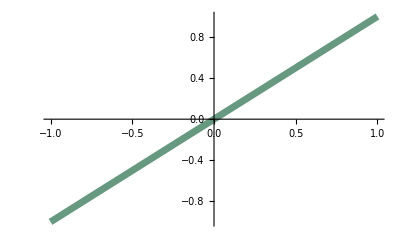

```mathematica
Plot[x,{x,-1,1},ColorFunction->CoolColor,ColorFunctionScaling->False,PlotStyle->AbsoluteThickness[5]]
```

```mathematica
Manipulate[
Show[
Graphics3D[{PointSize[.03],Red,With[{pt={Cos[p]Sin[t],Sin[p]Sin[t],Cos[t]}f[t,p]},Point[pt,VertexNormals->pt]]}],
SphericalPlot3D[
f[θ,ϕ],{θ,0,Pi},{ϕ,0,2Pi},
Mesh->False,PlotPoints->{60,10},ColorFunction -> (CoolColor[#6]&),ColorFunctionScaling->False
],
(*SphericalPlot3D[
1,
{p,0,2 Pi},{t,0,Pi},
Mesh->False,PlotStyle->Directive[Gray,Opacity[.25]]],*)
ViewAngle->Automatic,SphericalRegion->True,Ticks->None,PlotRange->All,AxesOrigin->{0,0,0},Boxed->False,PlotLabel->N[f[t,p]]
],{{t,0,"Θ"},0,π,π/12,Appearance->"Labeled"},{{p,0,"ϕ"},0,2π,π/12,Appearance->"Labeled"}
]
```

```mathematica
Export["C:\\Documents and Settings\\Milan Hanuš\\Dokumenty\\FAV\\Diplomka\\thesis\\pic\\sh.eps",GraphicsGrid[Table[Table[ParametricPlot3D[
Evaluate[{Cos[p]Sin[t],Sin[p]Sin[t],Cos[t]}Abs[Re[SphericalHarmonicY[l,m,t,p]]]],
{p,0,2 Pi},{t,0,Pi},PlotRange->{{-.45,.45},{-.45,.45},{-0.775,0.775}},
Mesh->False,PlotPoints->{36,18},MaxRecursion->2,
ViewAngle->Automatic,Axes->True,SphericalRegion->False,Boxed->False,AxesOrigin->{0,0,0},Ticks->None,ColorFunction -> Function[{x,y,z,p,t},Piecewise[{{RGBColor[0,1,0], Evaluate[Re[SphericalHarmonicY[l,m,t,p]]]>  0}, {RGBColor[0,0,1], Evaluate[Re[SphericalHarmonicY[l,m,t,p]]]==  0}, {RGBColor[1,0,0], Evaluate[Re[SphericalHarmonicY[l,m,t,p]]]< 0}}]],ColorFunctionScaling->False,PlotLabel->Style[With[{l=l,m=Round@m},TraditionalForm[HoldForm[Abs[Re[SphericalHarmonicY[l,m,θ,ϕ]]]]]],8]],
{m,-l,l,1}],{l,0,3,1}],ImageSize->Scaled[1.25]],ImageResolution->600]
```

C:\Documents and Settings\Milan Hanuš\Dokumenty\FAV\Diplomka\thesis\pic\sh.eps